## Plot of x(t) for respectively: ωτ << 1, ωτ ~ 2π, ωτ >> 1:: (0<t<τ)

1

2

1

5

0

0.001

2.25

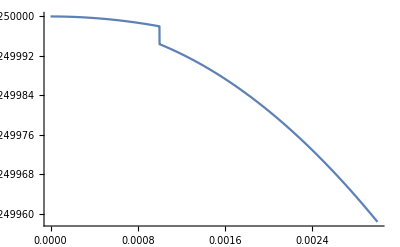

```mathematica
Subscript[x, 0]=1
w=2
m=1
F=5
ϕ=0
τ=0.001
B=√((Subscript[x, 0]*Sin[w*τ+ϕ])^2+(Subscript[x, 0]*Cos[w*τ+ϕ]+F/(m*w^2))^2)

Plot[Piecewise[{{Subscript[x, 0]*Cos[w*t+ϕ]+F/(m*w^2),0<t<τ},{B*Cos[w*t+ϕ],t>τ}}],{t,0,3τ},PlotRange->All]
```

π

9/4

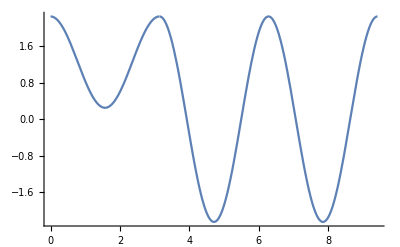

```mathematica
τ=2*Pi/w
B=√((Subscript[x, 0]*Sin[w*τ+ϕ])^2+(Subscript[x, 0]*Cos[w*τ+ϕ]+F/(m*w^2))^2)

Plot[Piecewise[{{Subscript[x, 0]*Cos[w*t+ϕ]+F/(m*w^2),0<t<τ},{B*Cos[w*t+ϕ],t>τ}}],{t,0,3τ},PlotRange->All]
```

500

√((5/4+Cos[1000])^2+Sin[1000]^2)

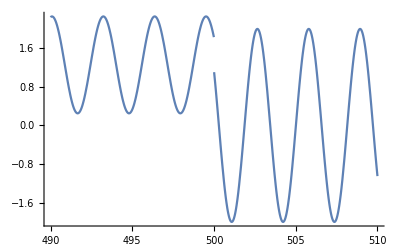

```mathematica
τ=500
B=√((Subscript[x, 0]*Sin[w*τ+ϕ])^2+(Subscript[x, 0]*Cos[w*τ+ϕ]+F/(m*w^2))^2)

Plot[Piecewise[{{Subscript[x, 0]*Cos[w*t+ϕ]+F/(m*w^2),0<t<τ},{B*Cos[w*t+ϕ],t>τ}}],{t,490,510},PlotRange->All]
```

## plot of max(x(t)) vs ω as an animator with τ :

```mathematica
W=Abs[F*Subscript[x, 0]*(Cos[w*τ+ϕ]-Cos[ϕ])]
Manipulate[Plot[√(2*Abs[F*Subscript[x, 0]*(Cos[w*τ+ϕ]-Cos[ϕ])]/(m*w^2)),{w,0,15}],{τ,0,10}]
```

5 (1-Cos[1000])